```mathematica
par={R->1,k->1};
```

```mathematica
u=Sec[π/2 k(R-x)];
U=Piecewise[{
{u,x≥R},
{u/.x->R,x<R}}]//Simplify
```

Piecewise[{{Sec[1/2 k π (R-x)], x≥R}, {1, x<R}, {0, True}}]

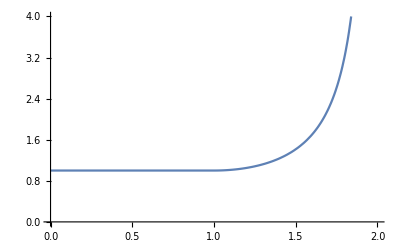

```mathematica
Plot[U/.par,
{x,0,R+1/k/.par},
PlotRange->{{0,R+1/k/.par},{0,4}}]
```

Piecewise[{{2 k π Csc[k π (R-x)]^2 Sin[1/2 k π (R-x)]^3, R≤x}, {0, True}}]

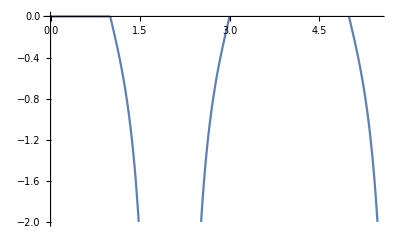

```mathematica
f=-D[U,x]//Simplify
Plot[f/.par//Evaluate,{x,0,6},
PlotRange->{{0,R+1/k/.par},{0,-2}}]
```

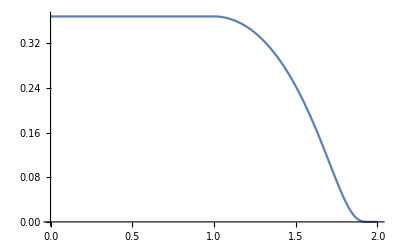

```mathematica
p=Exp[-U];
Plot[p/.par,
{x,0,R+1/k/.par}]
```

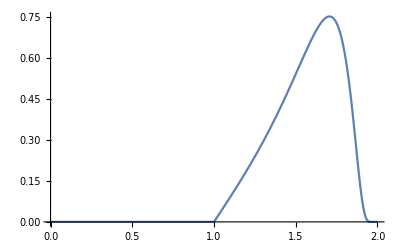

```mathematica
Plot[-p*f/.par,
{x,0,R+1/k/.par}]
```

```mathematica
Assuming[R>0&&k>0,Integrate[-p*f,{x,0,R+1/k}]]
```

$Aborted

```mathematica
Assuming[R>0&&k>0&&xx<R+1,Integrate[-p*f,{x,R,xx}]]
```

Piecewise[{{ⅇ^(-1-Sec[1/2 k π (R-xx)]) (-ⅇ+ⅇ^Sec[1/2 k π (R-xx)]), R>0&&R-xx<0}, {0, True}}]

```mathematica
Assuming[k>0,Integrate[Exp[-u],{x,0,1/k}]]
```

∫_0^(1/k) ⅇ^(-Sec[1/2 k π (R-x)])ⅆx

```mathematica
Assuming[k>0&&n∈Integers&&a>0,Integrate[Sec[a x]^n,x]]//FullSimplify
```

((Cos[a x]^2)^((1+n)/2) Hypergeometric2F1[1/2,(1+n)/2,3/2,Sin[a x]^2] Sec[a x]^(1+n) Sin[a x])/a

```mathematica
Sum[Hypergeometric2F1[1/2,(1+n)/2,3/2,y],{n,0,∞}]
```

∑_(n=0)^∞ Hypergeometric2F1[1/2,(1+n)/2,3/2,y]

```mathematica
Series[Sec[(π k)/2 x],{x,0,4}]
Series[Sec[(π k)/2 x],{x,1/k,4}]
```

1+1/8 k^2 π^2 x^2+5/384 k^4 π^4 x^4+O[x]^5

-2/((k π) (x-1/k))-1/12 (k π) (x-1/k)-(7 (k^3 π^3) (x-1/k)^3)/2880+O[x-1/k]^5

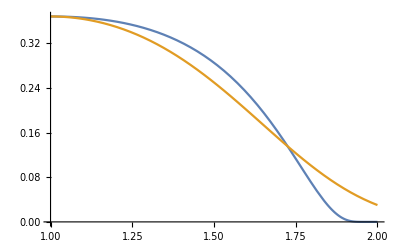

```mathematica
Plot[{p,1/ⅇ Exp[-(x-R)^2*1/8 k^2 π^2-(x-R)^4 5/384 k^4 π^4]}/.par//Evaluate,
{x,R/.par,R+1/k/.par}]
```

```mathematica
Manipulate[
Plot[p^e/.par//Evaluate,
{x,0,R+1/k/.par},PlotRange->All],
{e,0.1,10}]
```

```mathematica
Manipulate[Plot[-p^e*f/.par,
{x,0,R+1/k/.par},PlotRange->All],
{e,0.1,10}]
```

```mathematica
Assuming[l>0,Integrate[Exp[-Sec[x]^2],{x,0,π/2}]]
```

1/2 π Erfc[1]

```mathematica
par={R->1,k->0.5};
```

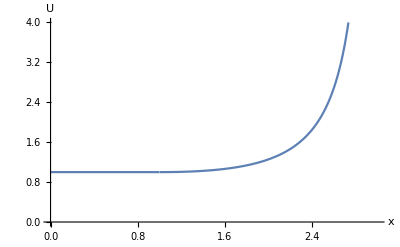

Piecewise[{{(k (1-Cosh[k (R-x)]+(1+k R-k x) Sinh[k (R-x)]))/(1+k (R-x))^2, R≤x}, {0, True}}]

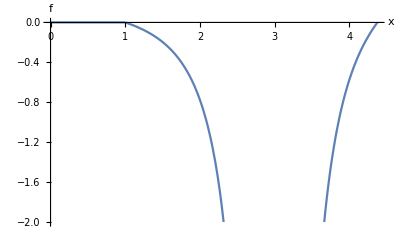

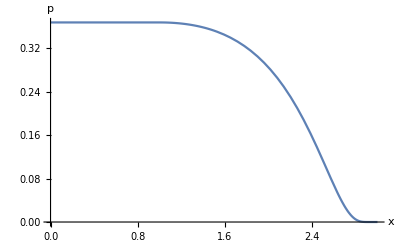

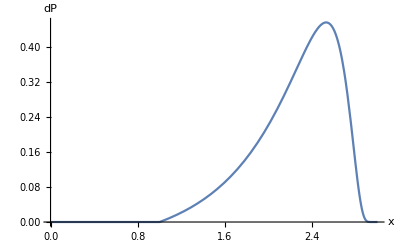

```mathematica
u=(Cosh[k(R-x)]-1)/(k(R-x)+1)+1;
U=Piecewise[{
{u,x≥R},
{u/.x->R,x<R}}]//Simplify;
Plot[{U}/.par//Evaluate,
{x,0,R+1/k/.par},
PlotRange->{{0,R+1/k/.par},{0,4}},
AxesLabel->{"x","U"}]
f=-D[U,x]//Simplify
Plot[f/.par//Evaluate,{x,0,6},
PlotRange->{{0,R+1/k/.par},{0,-2}},
AxesLabel->{"x","f"}]
p=Exp[-U];
Plot[p/.par,
{x,0,R+1/k/.par},
AxesLabel->{"x","p"}]
Plot[-p*f/.par,
{x,0,R+1/k/.par},
AxesLabel->{"x","dP"}]
```

```mathematica
Assuming[R>0&&k>0,Integrate[-p*f,{x,0,R+1/k}]]
```

$Aborted